```mathematica
CC
```

所有临时定义已清空!

```mathematica
CC
```

所有临时定义已清空!

```mathematica
limit=100;

degofunsat[c_Integer,h_Integer,n_Integer]:=(2*c+2-h+n)/2; (*Degrees of Unsaturation*)
Solver[a_Integer,b_Integer,c_Integer:0,d_Integer:0]:=Block[
{solutionList={},deg = degofunsat[a,b,c],buildrecur},
(*If[!IntegerQ@deg,Return@$Failed];*)
buildrecur[nC_Integer,nH_Integer,nO_Integer,nN_Integer,curM_,cMap_,tC_,tH_,tO_,tN_,dg_,dU_] :=
Module[{tM,sortM,fB,fB2},
If[Length[solutionList]<limit,
If[nC==nH==nO==nN==0&&Total[curM[[All,1]]]==0,
solutionList=Append[solutionList,cMap],
If[nC+nH+nO+nN>0 && Total[curM[[All,1]]] >0,
sortM=Reverse[Sort[curM]];
fB:=sortM[[1,1]];
If[fB≥1&&nC>0,
tM=Append[sortM,{3,{"C",tC}}];(*C1*)
tM[[1,1]]-=1;
buildrecur[nC-1,nH,nO,nN,tM,Append[cMap,{"C",tC}<-> sortM[[1,2]]],tC+1,tH,tO,tN,dg,dU]];
If[fB≥1&&nO>0,
tM=Append[sortM,{1,{"O",tO}}];(*O1*)
tM[[1,1]]-=1;
buildrecur[nC,nH,nO-1,nN,tM,Append[cMap,{"O",tO}<-> sortM[[1,2]]],tC,tH,tO+1,tN,dg,dU]];
If[fB≥1&&nH>0,
tM=Append[sortM,{0,{"H",tH}}];(*H1*)
tM[[1,1]]-=1;
buildrecur[nC,nH-1,nO,nN,tM,Append[cMap,{"H",tH}<-> sortM[[1,2]]],tC,tH+1,tO,tN,dg,dU];];
If[fB≥1&&nN>0,
tM=Append[sortM,{2,{"N",tN}}];(*C1*)
tM[[1,1]]-=1;
buildrecur[nC,nH,nO,nN-1,tM,Append[cMap,{"N",tN}<-> sortM[[1,2]]],tC,tH,tO,tN+1,dg,dU]];
If[fB≥1&&Length[sortM]≥2&&sortM[[2,1]]≥1&&dg-dU≥1,
tM=sortM;
tM[[1,1]]-=1;
tM[[2,1]]-=1;
buildrecur[nC,nH,nO,nN,tM,Append[cMap,sortM[[1,2]]<-> sortM[[2,2]]],tC,tH,tO,tN,dg,dU+1]];
If[fB≥2&&nC>0&&dg-dU≥1,
tM=Append[sortM,{2,{"C",tC}}];(*C2*)
tM[[1,1]]-=2;
buildrecur[nC-1,nH,nO,nN,tM,Append[Append[cMap,{"C",tC}<-> sortM[[1,2]]],{"C",tC}<-> sortM[[1,2]]],tC+1,tH,tO,tN,dg,dU+1]];
If[fB≥2&&nO>0&&dg-dU≥1,
tM=Append[sortM,{0,{"O",tO}}];(*O2*)
tM[[1,1]]-=2;
buildrecur[nC,nH,nO-1,nN,tM,Append[Append[cMap,{"O",tO}<-> sortM[[1,2]]],{"O",tO}<-> sortM[[1,2]]],tC,tH,tO+1,tN,dg,dU+1]];
If[fB≥2&&nN>0&&dg-dU≥1,
tM=Append[sortM,{1,{"N",tN}}];(*C2*)
tM[[1,1]]-=2;
buildrecur[nC,nH,nO,nN-1,tM,Append[Append[cMap,{"N",tN}<-> sortM[[1,2]]],{"N",tN}<-> sortM[[1,2]]],tC,tH,tO,tN+1,dg,dU+1]];
If[fB≥3&&nC>0&&dg-dU≥2,
tM=Append[sortM,{1,{"C",tC}}];(*C3*)
tM[[1,1]]-=3;
buildrecur[nC-1,nH,nO,nN,tM,Append[Append[Append[cMap,{"C",tC}<-> sortM[[1,2]]],{"C",tC}<-> sortM[[1,2]]],{"C",tC}<-> sortM[[1,2]]],tC+1,tH,tO,tN,dg,dU+2]];
If[fB≥3&&nN>0&&dg-dU≥2,
tM=Append[sortM,{0,{"N",tN}}];(*C3*)
tM[[1,1]]-=3;
buildrecur[nC,nH,nO,nN-1,tM,Append[Append[Append[cMap,{"N",tN}<-> sortM[[1,2]]],{"N",tN}<-> sortM[[1,2]]],{"N",tN}<-> sortM[[1,2]]],tC,tH,tO,tN+1,dg,dU+2]];
]]]
];
buildrecur[a-1,b,c,d,{{4,{"C",1}}},{},2,1,1,1,deg,0];
Return[solutionList]
]

solutionList=Solver[2,4,1,0]
```

{{{C,2}<->{C,1},{O,1}<->{C,2},{H,1}<->{C,1},{H,2}<->{C,2},{H,3}<->{C,1},{O,1}<->{C,2},{H,4}<->{C,1}},{{C,2}<->{C,1},{O,1}<->{C,2},{H,1}<->{C,1},{H,2}<->{C,2},{C,1}<->{O,1},{H,3}<->{C,2},{H,4}<->{C,1}},81,{{O,1}<->{C,1},{O,1}<->{C,1},{C,2}<->{C,1},{H,1}<->{C,2},{H,2}<->{C,2},{H,3}<->{C,2},{H,4}<->{C,1}},{{O,1}<->{C,1},{O,1}<->{C,1},{H,1}<->{C,1},{C,2}<->{C,1},{H,2}<->{C,2},{H,3}<->{C,2},{H,4}<->{C,2}}}
 |  |  |  |

False

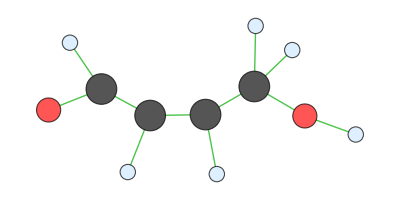
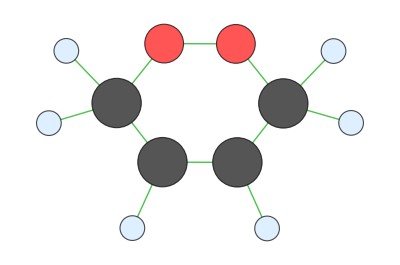
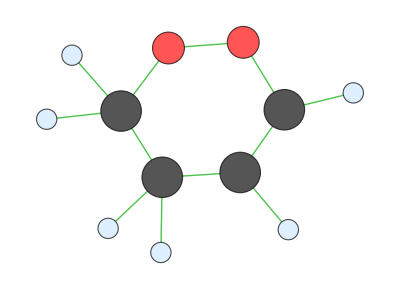
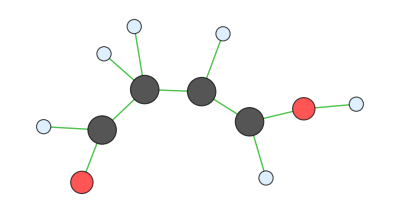
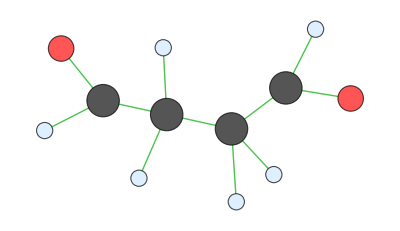
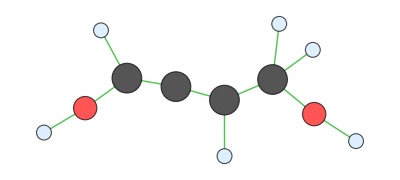
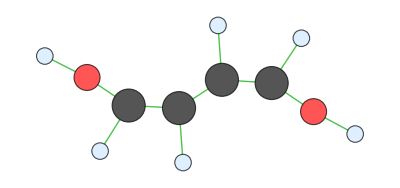
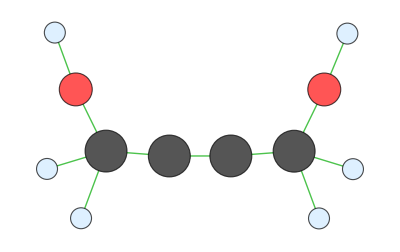

```mathematica
IntegerQ[deg] &&deg≥0 &&(nH+nO+nN)≥1&&nC+nH+nO+nN≥1&&!(nC==1 && ((nO≠ 2&&nH==nN==0)||(nN>1 && nH==nO==0)))

solutionList=Solver[4,6,2,0];

graphs=Graph/@DeleteDuplicates/@Map[Sort,solutionList,2];

atomToNumber=<|"H"->1,"C"->2,"O"->3,"N"->4|>;

del=DeleteDuplicatesBy[graphs,IGBlissCanonicalGraph[{#,"VertexColors"->"Color"}]&@*IGVertexMap[atomToNumber@*First,"Color"->VertexList]@*SimpleGraph];


show=Graph[#, GraphLayout->"SpringEmbedding",
VertexStyle->{{"C",_}->Lighter[Black],{"O",_}->Lighter[Red],{"H",_}->LightBlue,{"N",_}-> Lighter[Blue]},
EdgeStyle-> Darker@Green,VertexSize->{{"C",_}->0.7,{"O",_}->0.55,{"H",_}->0.35,{"N",_}->0.6}
]&;
show/@del
```